```mathematica
SetDirectory@NotebookDirectory[];
```

## Parameters

```mathematica
Nq=10;
```

## Data

```mathematica
path="data/Heisenberg-Chain-Nq="<>ToString[Nq]<>".dat";
file=File[path];
Data=Import[file];
γHC=Data[[2;;8]];
Length[Transpose[γHC]]
(*γHC={{},{},{},{},{},{},{}};*)
```

8

```mathematica
path="data/Heisenberg-Ladder-Nq="<>ToString[Nq]<>".dat";
file=File[path];
Data=Import[file];
γHL=Data[[2;;8]];
Length[Transpose[γHL]]
(*γHL={{},{},{},{},{},{},{}};*)
```

7

```mathematica
γHR={};
Do[(
path="data/Heisenberg-Random-Nq="<>ToString[Nq]<>"-"<>ToString[l]<>".dat";
file=File[path];
Data=Import[file];
γHR=Join[γHR,Transpose[Data[[2;;8]]]]
),{l,1,5}]
γHR=Transpose[γHR];
(*γHR={{},{},{},{},{},{},{}};*)
```

```mathematica
path="data/FermiHubbard-Chain-Nq="<>ToString[Nq]<>".dat";
file=File[path];
Data=Import[file];
γFHC=Data[[2;;8]];
Length[Transpose[γFHC]]
(*γFHC={{},{},{},{},{},{},{}};*)
```

10

```mathematica
path="data/FermiHubbard-Ladder-Nq="<>ToString[Nq]<>".dat";
file=File[path];
Data=Import[file];
γFHL=Data[[2;;8]];
Length[Transpose[γFHL]]
(*γFHL={{},{},{},{},{},{},{}};*)
```

8

```mathematica
γFHR={};
Do[(
path="data/FermiHubbard-Random-Nq="<>ToString[Nq]<>"-"<>ToString[l]<>".dat";
file=File[path];
Data=Import[file];
γFHR=Join[γFHR,Transpose[Data[[2;;8]]]]
),{l,1,5}]
γFHR=Transpose[γFHR];
(*γFHR={{},{},{},{},{},{},{}};*)
```

## Comparison

```mathematica
γMin=1.*^-4;
γMax=Max[Flatten[Flatten[{γHC,γHL,γHR,γFHC,γFHL,γFHR}]]]
γMax=10.^Ceiling[Log10[γMax]];
PR={{γMin,γMax},{γMin,γMax}};
plot=ListLogLogPlot[{{{γMin,γMin},{γMax,γMax}},{{γMin,10.},{γMax,10.}}},PlotRange->PR,Joined->True,PlotStyle->{Gray,Cyan}];
```

7.38587×10^20

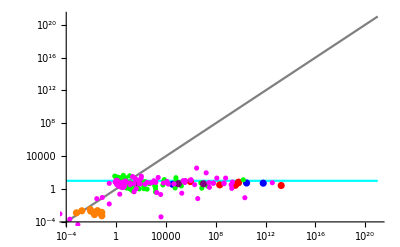

```mathematica
b=7;
plotHC=ListLogLogPlot[Transpose[{γHC[[b]],γHC[[3]]}],PlotRange->Full,PlotStyle->{Red}];
plotHL=ListLogLogPlot[Transpose[{γHL[[b]],γHL[[3]]}],PlotRange->Full,PlotStyle->{Blue}];
plotHR=ListLogLogPlot[Transpose[{γHR[[b]],γHR[[3]]}],PlotRange->Full,PlotStyle->{Green}];
plotFHC=ListLogLogPlot[Transpose[{γFHC[[b]],γFHC[[3]]}],PlotRange->Full,PlotStyle->{Orange}];
plotFHL=ListLogLogPlot[Transpose[{γFHL[[b]],γFHL[[3]]}],PlotRange->Full,PlotStyle->{Purple}];
plotFHR=ListLogLogPlot[Transpose[{γFHR[[b]],γFHR[[3]]}],PlotRange->Full,PlotStyle->{Magenta}];
Show[{plot,plotHC,plotHL,plotHR,plotFHC,plotFHL,plotFHR}]
```

## Empirical Distribution

```mathematica
γList={};
γList=Join[γList,Transpose[γHC]];
γList=Join[γList,Transpose[γHL]];
γList=Join[γList,Transpose[γHR]];
γList=Join[γList,Transpose[γFHC]];
γList=Join[γList,Transpose[γFHL]];
γList=Join[γList,Transpose[γFHR]];
Length[γList]
γList=Transpose[γList];
```

233

```mathematica
γMax=1.*^15;
Do[(
Do[If[γList[[b,i]]==0.||Abs[γList[[b,i]]]>γMax,γList[[b,i]]=2.*γMax],{i,1,Length[γList[[b]]]}]
),{b,1,7}]
γMin=Min[Flatten[γList]]
γMin=10.^Floor[Log10[γMin]]
```

0.0000145445

0.00001

1.05795×10^7

2.×10^15

4.38356

{1,0.995708}

7.45311×10^8

8.76573×10^6

7.56026×10^12

12.97

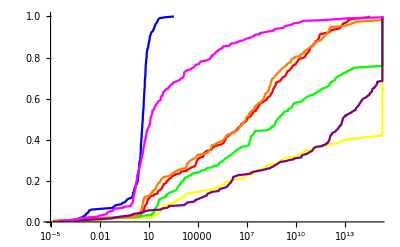

```mathematica
curves={};
Do[(
γ=γList[[b]];
γ=Sort[γ];
AppendTo[curves,Transpose[{γ,Table[i/Length[γ],{i,1,Length[γ]}]}]];
Print[(γ[[Floor[Length[γ]/2]]]+γ[[Ceiling[Length[γ]/2]]])/2];
If[b==3,(
pro=0;
Do[(
If[γ[[i]]≤100,pro=i]
),{i,1,Length[γ]}];
Print[{Length[γ]-pro,N[pro/Length[γ]]}]
)]
),{b,1,7}]

PR={{γMin,γMax},{0,1}};
ListLogLinearPlot[curves,PlotRange->PR,Joined->True,PlotStyle->{Red,Yellow,Blue,Green,Orange,Purple,Magenta}]
```

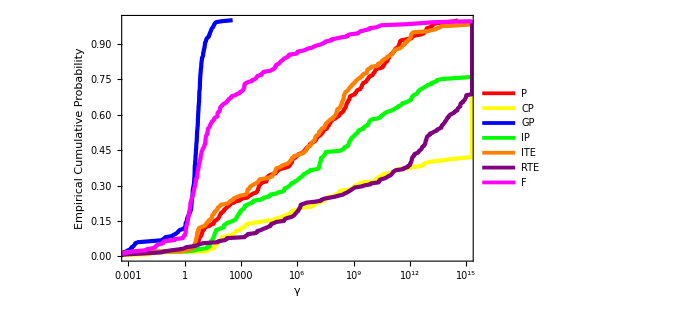

```mathematica
PR={{1.*^-3,1.*^15},{0,1}};
Fig=ListLogLinearPlot[curves,PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.006],Red},{Thickness[0.006],Yellow},{Thickness[0.006],Blue},{Thickness[0.006],Green},{Thickness[0.006],Orange},{Thickness[0.006],Purple},{Thickness[0.006],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],PlotLegends->Placed[LineLegend[{"P","CP","GP","IP","ITE","RTE","F"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->Directive[Black,Bold,FontSize->12,FontFamily->"Arial"],LegendMargins->0],{0.09,0.68}],FrameLabel->{"γ","Empirical Cumulative Probability"},LabelStyle->Directive[Black,FontSize->18,FontFamily->"Arial"],ImageSize->500]
```

```mathematica
Export["C:\\Users\\John\\Desktop\\Revise\\distribution.pdf",Fig];
```